```mathematica
DateString[]
SetDirectory[NotebookDirectory[]]
```

Wed 11 Mar 2026 10:33:49

D:\titimbo\SingleSG_Xukun2025

```mathematica
dataExp = Transpose[{10^-3{0.0,11.620000000000001,15.32,19.98,25.53,32.7,41.87,52.9,67.5,85.88,109.2,142.3,179.1,229.6,292.90000000000003,374.0,479.0,613.0,695.0,782.0,890.0,944.0},
10^-4{21.921273974326578,76.68738542882397,94.96685685569611,116.74315632617501,148.26719260132444,187.96802228364228,236.46350596358872,308.33909740360616,409.66166180382794,532.2938436243059,688.2773513962201,939.2339196003039,1228.044308107841,1636.9497049810138,2152.0745381309894,2808.5711301481842,3649.623990396425,4670.618880949969,5260.813765536719,5828.916846178714,6451.293060726494,6725.169618954149}}];
```

```mathematica
data1 = Import["SG_BvsI.csv"];
data2 = Sort[Import["SG_BvsI_phywe.csv"],#1[[1]]<#2[[1]]&];
```

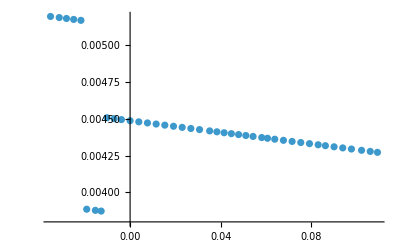

```mathematica
ListPlot[data2[[;;42,;;]],PlotRange->All]
```

FittedModel[…]

0.0044482

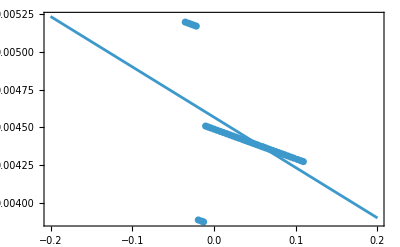

FittedModel[…]

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0044482 | 0.0000479816 | 92.7064 | 2.89795×10^-49,0.995252,0.995136}

```mathematica
datafit1=data2[[;;42,;;]];
lf1=LinearModelFit[datafit1,x,x]
Mean[datafit1[[;;,2]]]
Show[ListPlot[datafit1],Plot[lf1[x],{x,-0.2,0.2}],Frame->True,PlotRange->All]
nlm1=NonlinearModelFit[datafit1,a,a,x]
nlm1[{"ParameterTable","RSquared","AdjustedRSquared"}]
```

FittedModel[…]

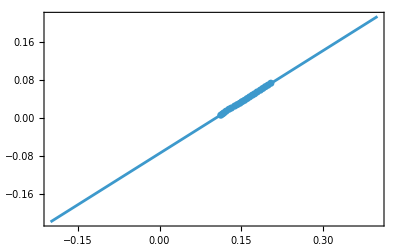

{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.0752333 | 0.000608687 | -123.599 | 4.48559×10^-29
b | 0.722926 | 0.00382689 | 188.907 | 1.42631×10^-32,0.999879,0.999867}

```mathematica
datafit2=data2[[43;;63,;;]];
lf2=LinearModelFit[datafit2,x,x]
Show[ListPlot[datafit2],Plot[lf2[x],{x,-0.2,0.4}],Frame->True,PlotRange->All]
nlm2=NonlinearModelFit[datafit2,a+b x,{a,b},x];
nlm2[{"ParameterTable","RSquared","AdjustedRSquared"}]
```

```mathematica
Icutting = Solve[Normal[nlm2]==Normal[nlm1],x][[1,1,2]]
```

0.110221

```mathematica
data3 = Transpose[{data2[[;;,1]]-Icutting,data2[[;;,2]]-Normal[nlm1]}];
data3a = Transpose[{data2[[;;,1]]-Icutting,data2[[;;,2]]}];
```

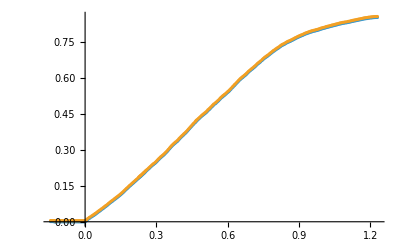

```mathematica
ListPlot[{data3,data3a}]
```

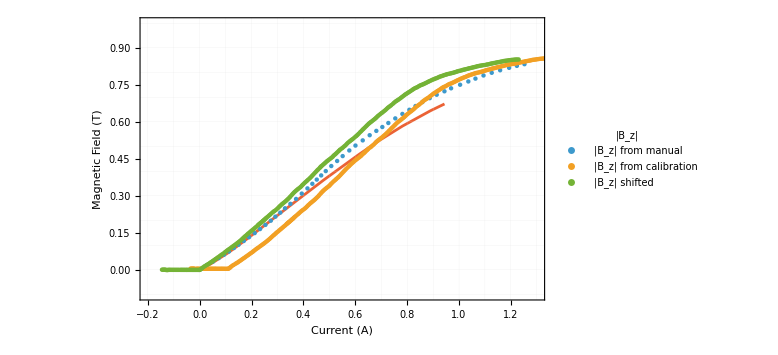

```mathematica
ListPlot[{data1,data2,data3,dataExp},
Frame->True,
Joined->{False,False,False,True},
PlotRange->{{-0.2,1.3},{-0.1,1.0}},
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->All,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| from calibration",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large]
```

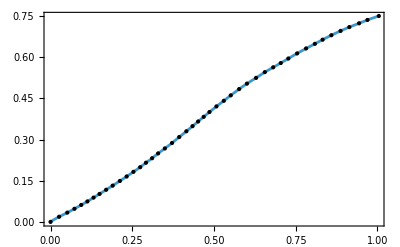

```mathematica
ifun1 = Interpolation[data1,InterpolationOrder->5];
Plot[ifun1[x],{x,0,1},Epilog->Point[data1],Frame->True]
```

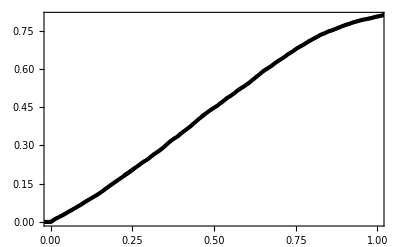

```mathematica
ifun3 = Interpolation[data3,InterpolationOrder->5];
Plot[ifun3[x],{x,0,1},Epilog->Point[data3],Frame->True]
```

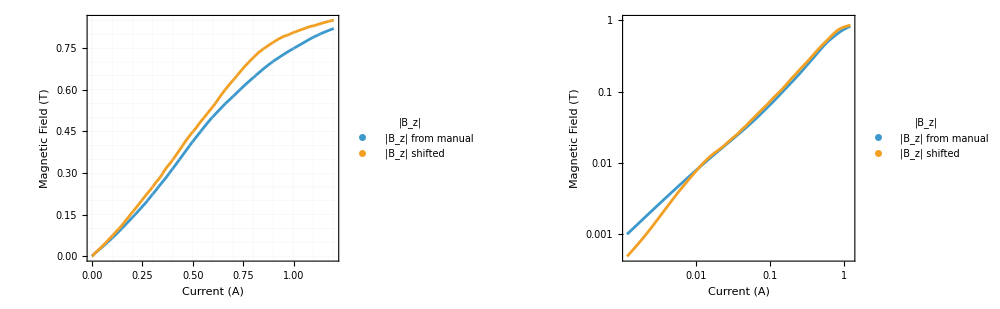

```mathematica
GraphicsRow[{
Plot[{ifun1[x],ifun3[x]},{x,0,1.2},
Frame->True,
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->All,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large],
LogLogPlot[{ifun1[x],ifun3[x]},{x,0,1.2},
Frame->True,
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large]
},ImageSize->1000]
```

```mathematica
(51.778*6.5)/(2 √(2Log[2]))
```

142.923